# Neural Networks

```mathematica
SetOptions[NetTrain,TargetDevice->"GPU"];
```

### Multilayer NN (two inputs, single output)

#### Learning “z=x^2+y^2”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->2],
ElementwiseLayer[Tanh],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->x.x,{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,result[{x,y}]},{x,-1,1},{y,-1,1},Mesh->None]
```

-Graphics3D-

Difference between learned curve and expected curve:

```mathematica
Plot3D[(x^2+y^2)-result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotRange->{Full,Full,{-.01,.01}}]
```

-Graphics3D-

#### Learning “z=Sin[3 x y]”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->2],
Tanh,
10,
Tanh,
DotPlusLayer[1,"Output"->"Scalar"]
}]
```

NetChain[]

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->Sin[3 First[x] Last[x]],{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
RandomSample[data,5]//Column
```

{-0.481225,-0.711269}→0.855668
{0.864305,-0.376864}→-0.828921
{-0.619433,0.83475}→-0.999808
{0.0119868,-0.0294798}→-0.00106011
{-0.312323,0.536423}→-0.481716

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[3 x y],result[{x,y}]},{x,-1,1},{y,-1,1},Mesh->None]
```

-Graphics3D-

Difference between learned curve and expected curve (error):

```mathematica
Plot3D[(Sin[3 x y])-result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotRange->{Full,Full,{-1,1}}]
```

-Graphics3D-

#### Learning “Sin[3 x y]>0”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->2],
Tanh,
10,
Tanh,
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->Boole[Sin[First[x] Last[x]]>0],{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
RandomSample[data,5]//Column
```

{-0.389846,0.394424}→0
{0.414325,-0.192447}→0
{0.599739,-0.690765}→0
{-0.636645,-0.864208}→1
{0.957451,-0.612587}→0

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

#### Learning “Sin[3 x y]>0”

```mathematica
net=NetChain[{
DotPlusLayer[40,"Input"->2],
Ramp,
40,
Ramp,
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->Boole[First[x] Last[x]>0],{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
RandomSample[data,5]//Column
```

{-0.447566,0.938668}→0
{0.449285,-0.967409}→0
{-0.944131,-0.672086}→1
{0.44284,0.775715}→1
{0.795319,-0.0170816}→0

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

### Multilayer NN (multiple inputs, multiple output)

#### 3 inputs to 3 outputs — learning to rotate lists of numbers

```mathematica
net=NetChain[{
DotPlusLayer[40,"Input"->3],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[3,"Output"->3]
}]
```

NetChain[]

```mathematica
net=NetInitialize[net];
```

```mathematica
data=#->RotateLeft[#]&/@RandomInteger[10,{10000,3}];
```

```mathematica
RandomSample[data,4]
```

{{10,3,7}→{3,7,10},{2,2,5}→{2,5,2},{2,2,3}→{2,3,2},{0,10,4}→{10,4,0}}

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[{2,2,5}]//Round
```

{2,5,2}

```mathematica
result[{1,2,3}]//Round
```

{2,3,1}

```mathematica
result[{8,7,6}]//Round
```

{7,6,8}

#### 20 inputs to 20 outputs — learning to rotate lists of numbers

Set up the neural network:

```mathematica
n=20;
net=NetChain[{
DotPlusLayer[4*n,"Input"->n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[4*n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[n,"Output"->n]
}];
```

Initialize the network with random values:

```mathematica
net=NetInitialize[net];
```

Set up the training data (here, generate lists of integers and rotate them by one element to the left):

```mathematica
data=#->RotateLeft[#]&/@RandomInteger[10,{10000,20}];
```

Train the neural network with the training data

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->300]
```

NetChain[]

Check the results of the trained neural network:

```mathematica
Table[
rr=RandomInteger[10,20];
{RotateLeft[rr],Round[result[rr]],SameQ[RotateLeft[rr],Round@result[rr]]}
,10]//Grid[#,Alignment->Left]&
```

{3,9,9,3,1,3,4,7,8,8,7,9,8,9,8,7,0,3,2,4} | {3,9,9,3,1,3,4,7,8,8,7,9,8,9,8,7,0,3,2,4} | True
{5,0,7,7,7,10,9,9,10,6,8,5,5,3,3,3,3,9,0,3} | {5,0,7,7,7,10,9,9,10,6,8,5,5,3,3,3,3,9,0,3} | True
{5,1,4,1,3,2,0,7,3,6,4,6,9,7,8,0,1,0,1,10} | {5,1,4,1,3,2,0,7,3,6,4,6,9,7,8,0,1,0,1,10} | True
{1,4,9,8,0,2,9,10,3,0,5,0,6,8,1,10,3,4,10,10} | {1,4,9,8,0,2,9,10,3,0,5,0,6,8,1,10,3,4,10,10} | True
{10,2,2,7,9,6,6,9,0,2,2,0,2,8,0,10,4,10,8,6} | {10,2,2,7,9,6,6,9,0,2,2,0,2,8,0,10,4,10,8,6} | True
{2,0,2,1,8,0,7,0,5,7,1,1,7,6,7,7,7,3,8,6} | {2,0,2,1,8,0,7,0,5,7,1,1,7,6,7,7,7,3,8,6} | True
{7,4,10,3,4,0,1,4,10,0,7,5,9,5,10,3,7,1,0,10} | {7,4,10,3,4,0,1,4,10,0,7,5,9,5,10,3,7,1,0,10} | True
{7,8,5,0,7,10,7,5,1,1,8,7,1,10,5,4,4,2,6,5} | {7,8,5,0,7,10,7,5,1,1,8,7,1,10,5,4,4,2,6,5} | True
{4,2,9,1,10,5,10,5,6,7,3,6,1,3,10,1,7,9,4,4} | {4,2,9,1,10,5,10,5,6,7,3,6,1,3,10,1,7,9,4,4} | True
{3,0,2,2,1,4,9,4,3,10,5,9,3,6,6,5,1,4,3,3} | {3,0,2,2,1,4,9,4,3,10,5,9,3,6,6,5,1,4,3,3} | True

#### 10 inputs to 10 outputs — learning to rotate lists of numbers

Set up the neural network:

```mathematica
n=10;
net=NetChain[{
DotPlusLayer[4*n,"Input"->n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[4*n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[n,"Output"->n]
}];
```

Initialize the network with random values:

```mathematica
net=NetInitialize[net];
```

Set up the training data (here, generate lists of integers and rotate them by one element to the left):

```mathematica
data=#->RotateLeft[#,6]&/@RandomInteger[10,{10000,n}];
```

Train the neural network with the training data

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->300]
```

NetChain[]

Check the results of the trained neural network:

```mathematica
Table[
rr=RandomInteger[10,n];
{RotateLeft[rr,6],Round[result[rr]],SameQ[RotateLeft[rr,6],Round@result[rr]]}
,10]//Grid[#,Alignment->Left]&
```

{4,2,3,6,9,9,5,6,0,4} | {4,2,3,6,9,9,5,6,0,4} | True
{3,9,0,3,10,4,1,9,8,3} | {3,9,0,3,10,4,1,9,8,3} | True
{2,4,1,2,8,1,0,7,4,1} | {2,4,1,2,8,1,0,7,4,1} | True
{8,3,2,5,10,6,7,5,10,7} | {8,3,2,5,10,6,7,5,10,7} | True
{5,2,5,6,1,4,3,8,9,9} | {5,2,5,6,1,4,3,8,9,9} | True
{7,6,1,5,5,10,5,4,2,9} | {7,6,1,5,5,10,5,4,2,9} | True
{7,8,10,4,8,1,9,3,7,7} | {7,8,10,4,8,1,9,3,7,7} | True
{10,7,9,2,4,5,3,8,9,7} | {10,7,9,2,4,5,3,8,9,7} | True
{3,3,1,5,7,7,6,2,10,6} | {3,3,1,5,7,7,6,2,10,6} | True
{3,2,7,5,0,0,0,9,4,9} | {3,2,7,5,0,0,0,9,4,9} | True

#### Going from 5 variables to 3

Define a nonlinear function from 5 variables (input) to 3 variables  (output):

```mathematica
f[v_List/;(Length[v]===5)]:={v[[1]]+v[[2]]^2,v[[3]]^2+v[[5]],v[[4]]^2}
```

Examples:

```mathematica
f[{1,2,3,4,5}]
```

{5,14,16}

```mathematica
f[{6,4,3,56,3}]
```

{22,12,3136}

Define a neural network that, hopefully, will train to the given function:

```mathematica
net=NetChain[{
DotPlusLayer[75,"Input"->5],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[75],
ElementwiseLayer[Tanh],
DotPlusLayer[3,"Output"->3]
}];
```

Initialize the neural network with random variables:

```mathematica
net=NetInitialize[net];
```

Generate a test data set to sample from (to learn from):

```mathematica
data=Table[x->f[x],{x,RandomInteger[10,{10000,5}]}];
```

Some sample data values:

```mathematica
RandomSample[data,10]//Column
```

{9,5,4,1,10}→{34,26,1}
{1,0,9,1,10}→{1,91,1}
{9,10,1,2,6}→{109,7,4}
{5,5,4,1,4}→{30,20,1}
{2,6,9,9,4}→{38,85,81}
{1,0,5,6,8}→{1,33,36}
{10,8,7,9,0}→{74,49,81}
{5,4,6,4,0}→{21,36,16}
{4,3,4,3,9}→{13,25,9}
{1,0,9,1,0}→{1,81,1}

Train the neural network on the given data set:

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->300]
```

NetChain[]

Check the results with a random input:

```mathematica
result[{7,9,4,1,7}]
```

{87.9362,23.1308,1.01788}

The feedforward pass will generate real numbers, but we want integer results (exact) in this case:

```mathematica
Round[result[{7,9,4,1,7}]]
```

{88,23,1}

Expected function value:

```mathematica
f[{7,9,4,1,7}]
```

{88,23,1}

This one is close to the expected result:

```mathematica
Round[result[{7,9,4,1,7}]]===f[{7,9,4,1,7}]
```

True

```mathematica
EuclideanDistance[f[{7,9,4,1,7}],result[{7,9,4,1,7}]]
```

0.146628

Check some more random examples, better results than before with a larger neural network:

```mathematica
Map[
{#,Round[result[#]],f[#],Round[result[#]]===f[#]}&,
RandomInteger[10,{20,5}]
]//Grid
```

{9,5,4,8,7} | {34,23,64} | {34,23,64} | True
{5,3,9,2,1} | {14,82,4} | {14,82,4} | True
{3,5,5,8,2} | {28,27,64} | {28,27,64} | True
{6,4,10,8,5} | {22,105,64} | {22,105,64} | True
{2,1,3,8,10} | {3,19,64} | {3,19,64} | True
{0,1,6,2,3} | {1,39,4} | {1,39,4} | True
{10,3,1,7,7} | {19,8,49} | {19,8,49} | True
{7,7,1,6,4} | {56,5,36} | {56,5,36} | True
{4,4,5,0,9} | {20,34,0} | {20,34,0} | True
{9,0,0,4,5} | {9,5,16} | {9,5,16} | True
{7,6,2,4,3} | {43,7,16} | {43,7,16} | True
{4,9,9,4,7} | {85,88,16} | {85,88,16} | True
{4,0,9,5,5} | {4,86,25} | {4,86,25} | True
{6,8,0,10,9} | {70,9,100} | {70,9,100} | True
{0,0,5,5,0} | {0,25,25} | {0,25,25} | True
{8,8,1,7,9} | {72,10,49} | {72,10,49} | True
{1,10,7,9,7} | {101,56,81} | {101,56,81} | True
{4,5,6,2,4} | {29,40,4} | {29,40,4} | True
{3,1,7,7,9} | {4,58,49} | {4,58,49} | True
{0,5,1,8,6} | {25,7,64} | {25,7,64} | True

### Classification of randomly distributed data

```mathematica
sample[x_,n_]:=RandomVariate[NormalDistribution[x,1],n]
```

```mathematica
sample[0,10]
```

{2.31046,0.337562,0.370874,0.0845009,0.107493,-0.357277,0.780195,1.67355,1.31491,0.229901}

```mathematica
clusters=sample[#,200]&/@{-4,0,4};
```

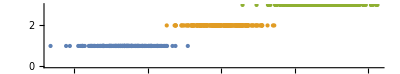

```mathematica
NumberLinePlot[clusters]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->"Scalar",
"Output"->NetDecoder[{"Class",{"a","b","c"}}]
]
```

NetChain[]

```mathematica
data=Join[Thread[clusters[[1]]->"a"],Thread[clusters[[2]]->"b"],Thread[clusters[[3]]->"c"]];
RandomSample[data,10]//Column
```

4.66593→c
4.43986→c
4.68359→c
-3.45999→a
-2.97519→a
3.10025→c
-0.465741→b
-1.87625→b
0.743842→b
4.44159→c

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[0]
```

b

```mathematica
result[0,"Probabilities"]
```

<|a→0.000288971,b→0.999458,c→0.000252558|>

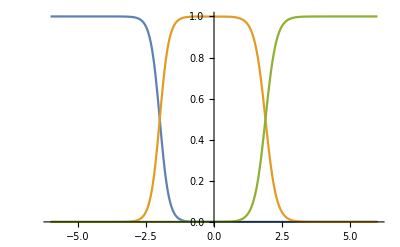

```mathematica
Plot[{
result[x,{"Probability","a"}],
result[x,{"Probability","b"}],
result[x,{"Probability","c"}]
},
{x,-6,6}
]
```

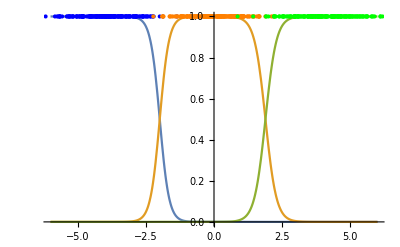

```mathematica
Show[
Plot[{
result[x,{"Probability","a"}],
result[x,{"Probability","b"}],
result[x,{"Probability","c"}]
},
{x,-6,6}
],
ListPlot[Map[{#,1}&,clusters,{2}],PlotStyle->{Blue,Orange,Green}]
]
```

### Classification of randomly distributed data (2)

```mathematica
sample[x_,n_]:=RandomVariate[NormalDistribution[x,1],n]
```

```mathematica
sample[0,10]
```

{0.150317,0.119591,-0.0489534,-0.122155,0.609375,0.0521476,0.162655,-0.193768,0.69005,-0.161387}

```mathematica
clusters=sample[#,200]&/@{-9,-4,-1,0,1,4,9};
```

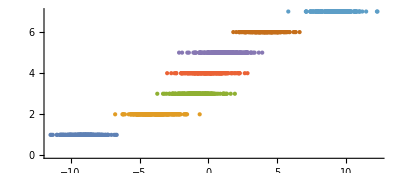

```mathematica
NumberLinePlot[clusters]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[7],
SoftmaxLayer[]
},
"Input"->"Scalar",
"Output"->NetDecoder[{"Class",{"a","b","c","d","e","f","g"}}]
]
```

NetChain[]

```mathematica
data=Join@@MapThread[Thread[#1->#2]&,{clusters,{"a","b","c","d","e","f","g"}}];
RandomSample[data,10]//Column
```

0.988099→d
-0.830487→d
0.672769→d
-0.347454→e
4.84934→f
-5.10326→b
4.18387→f
5.31361→f
0.575285→d
-9.80877→a

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[0]
```

d

```mathematica
result[0,"Probabilities"]
```

<|a→0.0000208822,b→0.000774317,c→0.30117,d→0.460378,e→0.237035,f→0.000613888,g→8.29448×10^-6|>

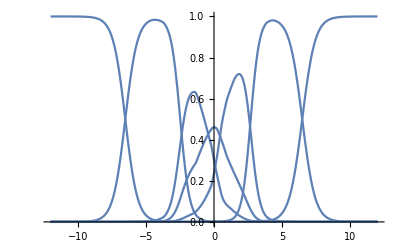

```mathematica
Plot[
Table[result[x,{"Probability",label}],{label,{"a","b","c","d","e","f","g"}}],
{x,-12,12},
PlotRange->All
]
```

### Classification of randomly distributed data (2 dimensions)

```mathematica
sampledata[center_]:=RandomVariate[MultinormalDistribution[center,IdentityMatrix[2]],200]
```

```mathematica
sampledata[{0,0}]
```

```mathematica
clusters=sampledata/@{{1.5,1},{-1.5,1},{0,-3}};
```

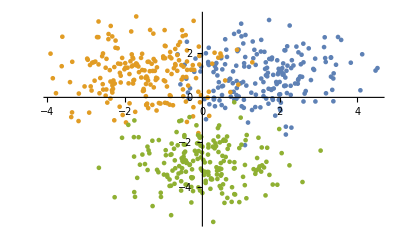

```mathematica
ListPlot[clusters,PlotTheme->"Minimal"]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{"a","b","c"}}]
]
```

NetChain[]

```mathematica
data=Join[Thread[clusters[[1]]->"a"],Thread[clusters[[2]]->"b"],Thread[clusters[[3]]->"c"]];
RandomSample[data,10]//Column
```

{-0.103942,-4.02271}→c
{0.145177,-2.55683}→c
{-0.153948,-2.53883}→c
{-0.56767,0.582231}→a
{0.167985,1.44794}→a
{-1.39038,-2.36405}→c
{1.11235,2.78866}→a
{2.60955,1.56607}→a
{-2.80387,1.57209}→b
{-0.404139,-2.90897}→c

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[{0,0}]
```

a

```mathematica
result[{0,0},"Probabilities"]
```

<|a→0.523027,b→0.466223,c→0.0107499|>

```mathematica
Show[
Plot3D[{
result[{x,y},{"Probability","a"}],
result[{x,y},{"Probability","b"}],
result[{x,y},{"Probability","c"}]
},
{x,-4,4},{y,-4,4},
Lighting->{{"Ambient", LightBlue}},
MeshFunctions->{#3&},
Mesh->4
],
ListPointPlot3D[Map[Append[#,1]&,clusters,{2}],PlotStyle->{Yellow,Blue,Green}]
]
```

-Graphics3D-

### Classification of randomly distributed data (2 dimensions) (2)

```mathematica
sample[c_,n_]:=RandomVariate[MultinormalDistribution[c,IdentityMatrix[2]],n]
```

```mathematica
sample[{0,0},10]
```

{{-0.95127,1.99608},{0.474495,3.45859},{-0.973764,0.0409259},{0.55833,-1.08703},{-1.76116,0.672121},{-0.408968,-0.688231},{0.107866,-0.243079},{1.4705,-0.0263558},{1.79575,-1.66355},{0.045237,-0.567441}}

```mathematica
clusters=sample[#,1000]&/@Table[3{Cos[2π n/5],Sin[2π n/5]},{n,0,4}];
```

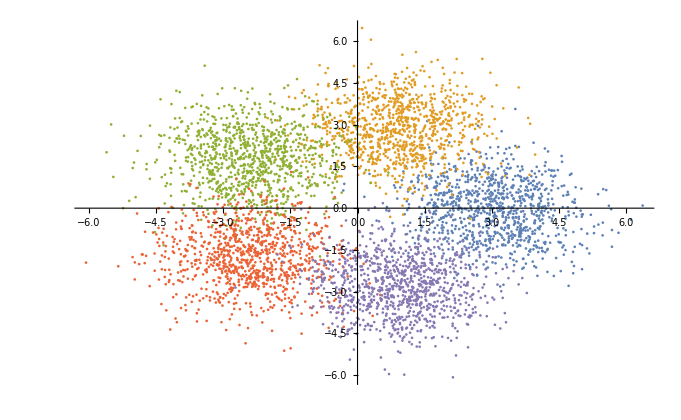

```mathematica
ListPlot[clusters,PlotTheme->"Minimal"]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[5],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{"a","b","c","d","e"}}]
]
```

NetChain[]

```mathematica
data=Join@@MapThread[Thread[#1->#2]&,{clusters,{"a","b","c","d","e"}}];
RandomSample[data,10]//Column
```

{-0.808625,-3.54768}→e
{-1.64044,-1.95408}→d
{0.647683,-3.78984}→e
{-2.82131,-2.85185}→d
{4.24522,-1.46392}→a
{0.922877,4.28191}→b
{-4.07803,2.39156}→c
{1.16486,-1.99217}→e
{4.3832,-2.43359}→a
{0.899893,-2.59813}→e

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[{0,0}]
```

e

```mathematica
result[{0,0},"Probabilities"]
```

<|a→0.276653,b→0.140567,c→0.180242,d→0.0526074,e→0.34993|>

```mathematica
Show[
Plot3D[{
result[{x,y},{"Probability","a"}],
result[{x,y},{"Probability","b"}],
result[{x,y},{"Probability","c"}],
result[{x,y},{"Probability","d"}],
result[{x,y},{"Probability","e"}]
},
{x,-6,6},{y,-6,6},
Lighting->{{"Ambient", LightBlue}},
MeshFunctions->{#3&},
Mesh->4
],
ListPointPlot3D[Map[Append[#,1]&,clusters,{2}],PlotStyle->{Yellow,Blue,Green,Orange,Purple}]
]
```

-Graphics3D-